```mathematica
(*************************)
(****** Milky Way ********)
(****** Parameters *******)
(*************************)
MWrs=(*17*)26 ;(* kpc *)
MWrhos=(*1.25 10^7*)3.87488 10^6 ;(* Msun / kpc^3 *)
MWNFW[r_]:=MWrhos/(r/MWrs(1+r/MWrs)^2);
```

```mathematica
(************************)
(****** conversion ******)
(************************)
 0.147328(* GeV /cm^3 *)(3.086 10^19(* m / kpc *) )^3(100 (* cm /m *))^3 (1.989 10^30(* kg / msol *))^-1(1.78 10^-27(* kg / GeV *))
```

3.87488×10^6

```mathematica
1.25 10^7(3.086 10^19(* m / kpc *) )^-3(100 (* cm /m *))^-3 (1.989 10^30(* kg / msol *))^1(1.78 10^-27(* kg / GeV *))^-1
```

0.475266

```mathematica
(*************************)
(********* M87 ***********)
(****** Parameters *******)
(*************************)
M87rs=(* 50.28 *) 20;(* kpc *)
M87rhos=(* 1.52 10^7 *) 6.57526  10^7;(* Msun / kpc^3 *)
M87NFW[r_]:=M87rhos/(r/M87rs(1+r/M87rs)^2);
```

```mathematica
(***********************)
(**** V0 Dispersion ****)
(***********************)
GNew=7 10^-20(1/(3 10^16))^3((2 10^30)/1)(*Newton's constant in kpc^3/(msol s^2)*);
```

```mathematica
VmaxM87=1.64 M87rs √(GNew  M87rhos); (* kpc / s *)
V0M87=VmaxM87/(√3) (* kpc / s *)
VmaxMW=1.64 MWrs √(GNew  MWrhos); (* kpc / s *)
V0MW=VmaxMW/(√3)(* kpc / s *)
```

1.10574×10^-14

3.48954×10^-15

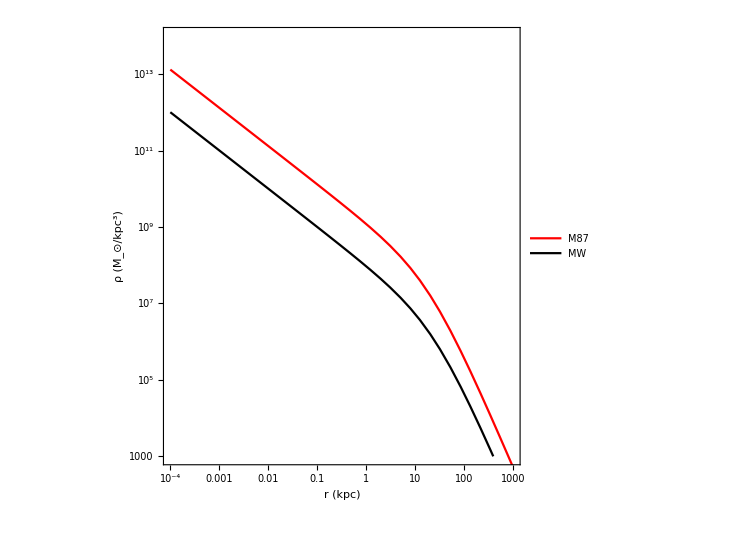

```mathematica
Show[LogLogPlot[MWNFW[r],{r,10^-4,10^6},PlotStyle->{Black},PlotRange->{{10^-4,10^3},{ 10^3,10^14}},PlotLegends-> Placed[LineLegend[{Red,Black},{"M87","MW"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.9,0.9}],FrameTicks->{{tPowerTicks[True],Automatic},{tPowerTicks[True],Automatic}}],LogLogPlot[M87NFW[r],{r,10^-4,10^6},PlotStyle->Red],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.0035],Black],FrameLabel-> {"r (kpc)",Row[{"ρ (",Subscript["M","⊙"],"/kpc^3)"}]},LabelStyle->Directive[Black,FontSize-> 25],AspectRatio-> 1]
```

```mathematica
(************************)
(******* J-Factor *******)
(************************)
DistMW= 8 (* 8 *);(* kpc *)
DistM87= 16 10^3;(* kpc *)
rMW[θ_,b_,s_]:=√(DistMW^2+s^2-2DistMW s Cos[θ]Cos[b]);
rM87[θ_,s_]:=√(DistM87^2+s^2-2DistM87 s Cos[θ]);
ρMW [θ_,b_,s_]=MWNFW[rMW[θ,b,s]];    
ρM87 [θ_,s_]=M87NFW[rM87[θ,s]]; 
θMax=π/180(5/10);
(*Off[NIntegrate::inumr]*)
funcMW[θ_,b_]=NIntegrate[ρMW[θ,b,s]^2,{s,0.1 DistMW,10DistMW}];
funcM87[θ_]= NIntegrate[ρM87[θ,s]^2,{s,DistM87-50,DistM87+50}] ;
```

```mathematica
JMWθ[θ_]= NIntegrate[funcMW[θ,b],{b,0,20 π/180}]; (* Msol^2 / kpc^5 *)
```

```mathematica
JMW=4NIntegrate[JMWθ[θ],{θ,0,20 π/180}]
```

6.33794×10^15

```mathematica
JM87=2π NIntegrate[Sin[θ]funcM87[θ],{θ,0,θMax}] (* Msol^2 / kpc^5 *)
```

5.61132×10^11

```mathematica
test=2 π NIntegrate[Sin[θ] ρM87[θ,s]^2,{s,DistM87-50,DistM87+50},{θ,0,θMax}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in s near {s,θ} = {16000.,6.7463×10^-8}. NIntegrate obtained 8.93828×10^10 and 4.42453×10^6 for the integral and error estimates.

5.61609×10^11

```mathematica
MWJFactor=JMW (* Msol^2 / kpc^5 *)(1/(3.086 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.78 10^-27(* kg / GeV *)))^2
```

2.82747×10^22

```mathematica
M87JFactor=JM87 (* Msol^2 / kpc^5 *)(1/(3.086 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.78 10^-27(* kg / GeV *)))^2
```

2.50331×10^18

```mathematica
(***********************)
(* Sphere of Influence *)
(***********************)
MWMbh=4 10^6; (* Msun *)
M87Mbh=6.4 10^9; (* Msun *)
NSolve[4π Integrate[r^2 MWNFW[r],{r,0,MWrbh},GenerateConditions->False]==2MWMbh,MWrbh]
NSolve[4π  Integrate[r^2 M87NFW[r],{r,0,M87rbh},GenerateConditions->False]==2M87Mbh,M87rbh]
```

{{MWrbh→-0.112096},{MWrbh→0.112744}}

{{M87rbh→-1.19469},{M87rbh→1.29807}}

```mathematica
0.1 MWrs(MWMbh/(MWrhos MWrs^3))^(1/2)
```

0.0199257

```mathematica
rspikeMW=(*(0.2)0.11*)0.0199257 (* kpc *)
rspikeM87=(*(0.2)1.20361*)0.2 (* kpc *)
rspikeMWalt=(GNew MWMbh)/V0MW^2 ;(* kpc *)
rspikeM87alt=(GNew M87Mbh)/V0M87^2 ;(* kpc *)
```

0.0199257

0.2

```mathematica
(**********************)
(**** Full Profile ****)
(**********************)
MW[r_]:=Piecewise[{{MWNFW[rspikeMW](rspikeMW/r)^(3/2),r<rspikeMW},{MWNFW[r],r≥ rspikeMW}}];
MWstar[r_]:=Piecewise[{{MWNFW[rspikeMW](rspikeMW/r)^(7/4),r<rspikeMW},{MWNFW[r],r≥ rspikeMW}}];
MWalt[r_]:=Piecewise[{{MWNFW[rspikeMWalt](rspikeMWalt/r)^(7/4),r<rspikeMWalt},{MWNFW[r],r≥ rspikeMWalt}}];
M87[r_]:=Piecewise[{{M87NFW[rspikeM87](rspikeM87/r)^(3/2),r<rspikeM87},{M87NFW[r],r≥ rspikeM87}}];
M87star[r_]:=Piecewise[{{M87NFW[rspikeM87](rspikeM87/r)^(7/4),r<rspikeM87},{M87NFW[r],r≥ rspikeM87}}];
M87alt[r_]:=Piecewise[{{M87NFW[rspikeM87alt](rspikeM87alt/r)^(7/4),r<rspikeM87alt},{M87NFW[r],r≥ rspikeM87alt}}];
```

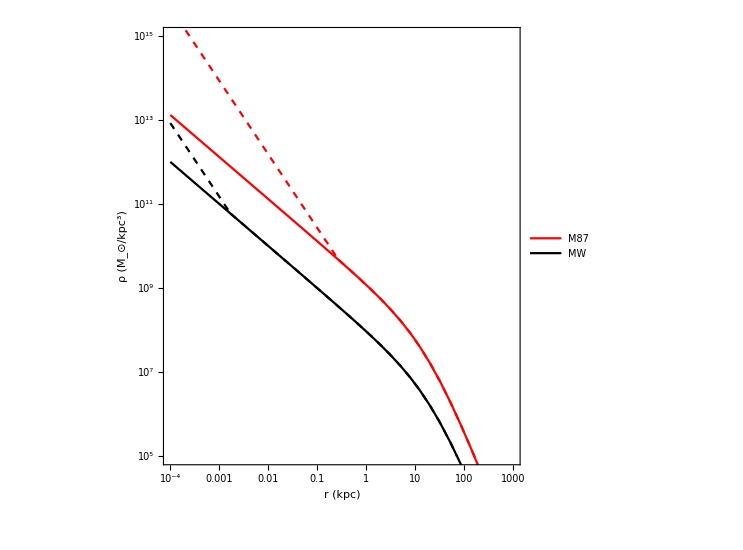

```mathematica
Show[LogLogPlot[MWalt[r],{r,10^-4,10^6},PlotStyle->{Black,Dashed},PlotRange->{{10^-4,10^3},{ 10^5,10^15}},PlotLegends-> Placed[LineLegend[{Red,Black},{"M87","MW"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.9,0.9}],FrameTicks->{{tPowerTicks[True],Automatic},{tPowerTicks[True],Automatic}}],
LogLogPlot[MWNFW[r],{r,10^-4,10^6},PlotStyle->{Black}],LogLogPlot[M87alt[r],{r,10^-4,10^6},PlotStyle->{Red,Dashed}],LogLogPlot[M87NFW[r],{r,10^-4,10^6},PlotStyle->{Red}],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.0035],Black],FrameLabel-> {"r (kpc)",Row[{"ρ (",Subscript["M","⊙"],"/kpc^3)"}]},LabelStyle->Directive[Black,FontSize-> 25],AspectRatio-> 1]
```

```mathematica
(********************)
(***** Q-Factor *****)
(***** γ = 3/2 ******)
(********************)
3 10^19;(* m / kpc *)
clight=3 10^8 (1/(3.086 10^19)); (* kpc /s *)
GNew=4.516 10^(-39)(*7.0 10^-20(1/(3 10^16))^3((2 10^30)/1)*)(*Newton's constant in kpc^3/(msol s^2)*)
rschMW=(2 GNew MWMbh)/clight^2;(* kpc *)
rschM87=(2 GNew M87Mbh)/clight^2 (* kpc *)
QMW=MW[rspikeMW]^2 rspikeMW^3 Log[rspikeMW/(2 rschMW)] (* Msol^2 / kpc^3 *)
QMWalt=MWalt[rspikeMWalt]^2 rspikeMWalt^3 Log[rspikeMWalt/(2 rschMW)] (* Msol^2 / kpc^3 *)
QM87=M87[rspikeM87]^2 rspikeM87^3 Log[rspikeM87/(2 rschM87)] (* Msol^2 / kpc^3 *)
QM87alt=M87alt[rspikeM87alt]^2 rspikeM87alt^3 Log[rspikeM87alt/(2 rschM87)] (* Msol^2 / kpc^3 *)
```

4.516×10^-39

6.11664×10^-7

3.44295×10^15

2.52628×10^14

3.99001×10^18

5.47473×10^18

```mathematica
(4π)/DistMW^2 QMW (* Msol^2 / kpc^5 *)
(4π)/DistMW^2 QMWalt(* Msol^2 / kpc^5 *)
(4π)/DistM87^2 QM87 (* Msol^2 / kpc^5 *)
(4π)/DistM87^2 QM87alt (* Msol^2 / kpc^5 *)
```

6.76022×10^14

4.96034×10^13

1.95859×10^11

2.6874×10^11

```mathematica
(4π)/DistMW^2 QMW (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
(4π)/DistMW^2 QMWalt (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2

(4π)/DistM87^2 QM87 (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
(4π)/DistM87^2 QM87alt (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

3.39687×10^21

2.49247×10^20

9.84153×10^17

1.35036×10^18

```mathematica
(**********************)
(****** Q Factor ******)
(****** γ > 3/2 *******)
(**********************)
QM87star[i_]:=(M87NFW[rspikeM87]^2 rspikeM87^(2i))/((2i-3)(2 rschM87)^(2i-3)); (* Msol^2 / kpc^3 *)
QM87staralt[i_]:=(M87NFW[rspikeM87alt]^2 rspikeM87alt^(2i))/((2i-3)(2rschM87)^(2i-3)); (* Msol^2 / kpc^3 *)
QMWstar[i_]:=(MWNFW[rspikeMW]^2 rspikeMW^(2i))/((2i-3)(2rschMW)^(2i-3));  (* Msol^2 / kpc^3 *)
QMWstaralt[i_]:=(MWNFW[rspikeMWalt]^2 rspikeMWalt^(2i))/((2i-3)(2rschMW)^(2i-3));  (* Msol^2 / kpc^3 *)
QMWstaralt[7/4]
```

5.15942×10^16

```mathematica
(***********************)
(**** bbbar Spectra ****)
(***********************)
xidata={{10,  9.99463},
{20, 14.0186},
{40, 18.6323},
{70, 23.015},
{100, 26.2174},
{200, 33.6505},
{400,43.0486},
{700, 52.2291},
{1000,  58.8666}};
xi=Interpolation[xidata,InterpolationOrder->3];
```

```mathematica
step=(Log10[10000]-Log10[10])/20;
stepin= Table[10^x,{x,Log10[10],Log10[10000],step}]
```

{10,10 10^(3/20),10 10^(3/10),10 10^(9/20),10 10^(3/5),10 10^(3/4),10 10^(9/10),100 10^(1/20),100 10^(1/5),100 10^(7/20),100 √10,100 10^(13/20),100 10^(4/5),100 10^(19/20),1000 10^(1/10),1000 10^(1/4),1000 10^(2/5),1000 10^(11/20),1000 10^(7/10),1000 10^(17/20),10000}

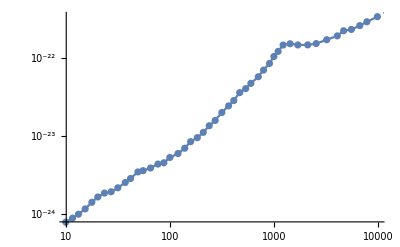

```mathematica
(************************)
(*** Upper Limit Flux ***)
(********* M87 **********)
(************************)
xlimitM87data={{9.914 10^0,7.766 10^-25},
{1.150 10^1,8.732 10^-25},
{1.312 10^1,9.821 10^-25},
{1.522 10^1,1.149 10^-24},
{1.765 10^1,1.398 10^-24},
{2.014 10^1,1.636 10^-24},
{2.335 10^1,1.839 10^-24},
{2.708 10^1,1.911 10^-24},
{3.141 10^1,2.149 10^-24},
{3.703 10^1,2.514 10^-24},
{4.156 10^1,2.827 10^-24},
{4.901 10^1,3.440 10^-24},
{5.499 10^1,3.575 10^-24},
{6.483 10^1,3.864 10^-24},
{7.644 10^1,4.344 10^-24},
{8.719 10^1,4.514 10^-24},
{9.948 10^1,5.282 10^-24},
{1.192 10^2,5.938 10^-24},
{1.383 10^2,6.946 10^-24},
{1.578 10^2,8.454 10^-24},
{1.830 10^2,9.506 10^-24},
{2.088 10^2,1.112 10^-23},
{2.383 10^2,1.354 10^-23},
{2.718 10^2,1.584 10^-23},
{3.153 10^2,2.005 10^-23},
{3.658 10^2,2.440 10^-23},
{4.105 10^2,2.856 10^-23},
{4.685 10^2,3.616 10^-23},
{5.344 10^2,4.066 10^-23},
{5.998 10^2,4.758 10^-23},
{7.073 10^2,5.790 10^-23},
{7.939 10^2,7.048 10^-23},
{9.058 10^2,8.579 10^-23},
{1.000 10^3,1.056 10^-22},
{1.098 10^3,1.228 10^-22},
{1.225 10^3,1.482 10^-22},
{1.432 10^3,1.541 10^-22},
{1.700 10^3,1.486 10^-22},
{2.116 10^3,1.489 10^-22},
{2.551 10^3,1.548 10^-22},
{3.225 10^3,1.736 10^-22},
{4.075 10^3,1.946 10^-22},
{4.690 10^3,2.264 10^-22},
{5.569 10^3,2.353 10^-22},
{6.716 10^3,2.638 10^-22},
{7.851 10^3,2.955 10^-22},
{9.922 10^3,3.440 10^-22},
{1.215 10^4,4.004 10^-22}}; (* {GeV, cm^3 / s} *)
xlimitM87=Interpolation[xlimitM87data,InterpolationOrder->1];(*cm^3 s^-1*)
Show[LogLogPlot[xlimitM87[x],{x,10,10000}],ListLogLogPlot[xlimitM87data]]
```

```mathematica
alphaM87[x_]:=1/2(1(*xi[x]*))/(4π x^2)M87JFactor(* GeV^2/cm^5 *);(* cm^-5 *) 
T=10 10^9(* yr *)((365(* day/yr*))/1)((24(* hr/day *))/1)((60 (* min/hr *))/1)((60(* s/min *))/1); (* s *)
```

```mathematica
fluxlimitM87[i_] :=NSolve[ alphaM87[i]  xlimitM87[i] ==y,y][[1]]
```

```mathematica
fluxlimitM87[10]
```

{y→7.7874×10^-10}

```mathematica
fluxDataM87= Table[{i,y/.fluxlimitM87[i][[1]]} ,{i,stepin}]
fluxM87=Interpolation[fluxDataM87] (* cm^-2 s^-1 *)
```

{{10,7.7874×10^-10},{10 10^(3/20),5.30153×10^-10},{10 10^(3/10),4.04835×10^-10},{10 10^(9/20),2.47235×10^-10},{10 10^(3/5),1.70069×10^-10},{10 10^(3/4),1.13754×10^-10},{10 10^(9/10),6.9322×10^-11},{100 10^(1/20),4.51384×10^-11},{100 10^(1/5),3.36367×10^-11},{100 10^(7/20),2.45566×10^-11},{100 √10,2.00501×10^-11},{100 10^(13/20),1.6624×10^-11},{100 10^(4/5),1.26525×10^-11},{100 10^(19/20),1.05079×10^-11},{1000 10^(1/10),9.3745×10^-12},{1000 10^(1/4),4.6823×10^-12},{1000 10^(2/5),2.43532×10^-12},{1000 10^(11/20),1.43665×10^-12},{1000 10^(7/10),9.10666×10^-13},{1000 10^(17/20),5.44438×10^-13},{10000,3.44603×10^-13}}

InterpolatingFunction[…]

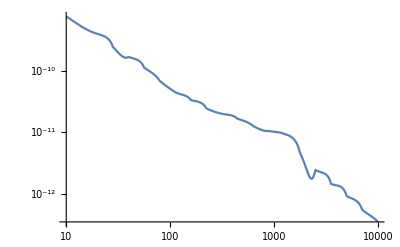

```mathematica
Show[LogLogPlot[fluxM87[x],{x,10,10000}],ListLogPlot[fluxDataM87]]
```

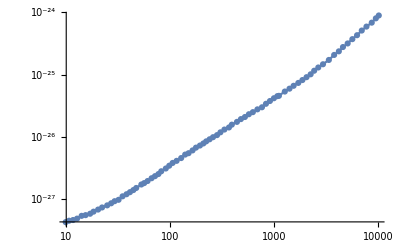

```mathematica
(******************************)
(****** Flux upper limit ******)
(************ MW **************)
(******************************)
xlimitMWdata={{9.875 10^0,4.184 10^-28},
{1.065 10^1,4.407 10^-28},
{1.163 10^1,4.524 10^-28},
{1.271 10^1,4.764 10^-28},
{1.406 10^1,5.283 10^-28},
{1.536 10^1,5.423 10^-28},
{1.699 10^1,5.712 10^-28},
{1.832 10^1,6.172 10^-28},
{2.027 10^1,6.670 10^-28},
{2.214 10^1,7.208 10^-28},
{2.480 10^1,7.790 10^-28},
{2.709 10^1,8.418 10^-28},
{2.922 10^1,9.096 10^-28},
{3.192 10^1,9.580 10^-28},
{3.487 10^1,1.090 10^-27},
{3.809 10^1,1.178 10^-27},
{4.109 10^1,1.272 10^-27},
{4.432 10^1,1.375 10^-27},
{4.720 10^1,1.486 10^-27},
{5.288 10^1,1.690 10^-27},
{5.632 10^1,1.780 10^-27},
{6.075 10^1,1.923 10^-27},
{6.636 10^1,2.132 10^-27},
{7.158 10^1,2.304 10^-27},
{7.721 10^1,2.490 10^-27},
{8.224 10^1,2.760 10^-27},
{9.097 10^1,3.060 10^-27},
{9.813 10^1,3.393 10^-27},
{1.058 10^2,3.761 10^-27},
{1.156 10^2,4.065 10^-27},
{1.279 10^2,4.507 10^-27},
{1.397 10^2,5.127 10^-27},
{1.507 10^2,5.399 10^-27},
{1.646 10^2,5.986 10^-27},
{1.775 10^2,6.637 10^-27},
{1.939 10^2,7.172 10^-27},
{2.092 10^2,7.749 10^-27},
{2.228 10^2,8.373 10^-27},
{2.403 10^2,9.047 10^-27},
{2.592 10^2,9.776 10^-27},
{2.832 10^2,1.056 10^-26},
{3.054 10^2,1.171 10^-26},
{3.336 10^2,1.298 10^-26},
{3.691 10^2,1.403 10^-26},
{3.931 10^2,1.556 10^-26},
{4.404 10^2,1.725 10^-26},
{4.811 10^2,1.913 10^-26},
{5.255 10^2,2.067 10^-26},
{5.740 10^2,2.291 10^-26},
{6.270 10^2,2.476 10^-26},
{6.936 10^2,2.746 10^-26},
{7.672 10^2,2.967 10^-26},
{8.381 10^2,3.375 10^-26},
{9.155 10^2,3.742 10^-26},
{1.000 10^3,4.149 10^-26},
{1.079 10^3,4.483 10^-26},
{1.117 10^3,4.533 10^-26},
{1.273 10^3,5.318 10^-26},
{1.412 10^3,5.916 10^-26},
{1.547 10^3,6.581 10^-26},
{1.717 10^3,7.321 10^-26},
{1.881 10^3,8.144 10^-26},
{2.061 10^3,9.060 10^-26},
{2.257 10^3,1.008 10^-25},
{2.441 10^3,1.151 10^-25},
{2.674 10^3,1.298 10^-25},
{2.968 10^3,1.463 10^-25},
{3.381 10^3,1.717 10^-25},
{3.801 10^3,2.068 10^-25},
{4.219 10^3,2.363 10^-25},
{4.621 10^3,2.772 10^-25},
{5.129 10^3,3.166 10^-25},
{5.693 10^3,3.715 10^-25},
{6.318 10^3,4.300 10^-25},
{7.012 10^3,5.113 10^-25},
{7.782 10^3,5.919 10^-25},
{8.750 10^3,6.852 10^-25},
{9.585 10^3,8.039 10^-25},
{1.023 10^4,8.942 10^-25}}; (* {GeV, cm^3/s } *)

xlimitMW=Interpolation[xlimitMWdata,InterpolationOrder->1];(*cm^-2 s^-1*)
Show[LogLogPlot[xlimitMW[x],{x,10,10000}],ListLogLogPlot[xlimitMWdata]]
```

```mathematica
alphaMW[x_]:=1/2(1(*xi[x]*))/(4π x^2)MWJFactor(* GeV^2/cm^5 *) ;  (* cm^-5 *)
```

```mathematica
fluxlimitMW[i_] :=NSolve[ alphaMW[i]  xlimitMW[i] ==y,y][[1]]
```

```mathematica
fluxDataMW= Table[{i,y/.fluxlimitMW[i][[1]]} ,{i,stepin}]
fluxMW=Interpolation[fluxDataMW] (* cm^-2 s^-1 *)
```

{{10,4.74753×10^-9},{10 10^(3/20),2.98275×10^-9},{10 10^(3/10),1.86198×10^-9},{10 10^(9/20),1.24156×10^-9},{10 10^(3/5),8.74459×10^-10},{10 10^(3/4),6.32456×10^-10},{10 10^(9/10),4.65249×10^-10},{100 10^(1/20),3.53841×10^-10},{100 10^(1/5),2.56541×10^-10},{100 10^(7/20),1.88876×10^-10},{100 √10,1.37225×10^-10},{100 10^(13/20),9.88995×10^-11},{100 10^(4/5),7.04229×10^-11},{100 10^(19/20),5.13699×10^-11},{1000 10^(1/10),3.72464×10^-11},{1000 10^(1/4),2.71393×10^-11},{1000 10^(2/5),2.13201×10^-11},{1000 10^(11/20),1.65918×10^-11},{1000 10^(7/10),1.37729×10^-11},{1000 10^(17/20),1.16357×10^-11},{10000,9.69763×10^-12}}

InterpolatingFunction[…]

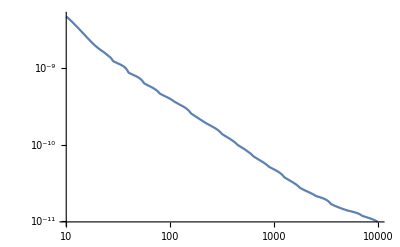

```mathematica
Show[LogLogPlot[fluxMW[x],{x,10,10000}],ListLogPlot[fluxDataMW]]
```

```mathematica
(******************)
(*** CDM Spike ****)
(******************)
rannMW[x_,y_]:=(((y T MWrhos ((1.989 10^30(* kg / msol *))/(1.8 10^-27(* kg / GeV *)))(1/(100 (* cm /m *))1/(3 10^19(* m / kpc *)))^3)/x MWrs)^3 rspikeMW^4)^(1/7) ; (* kpc *)     
QMWCDM[x_,y_]:=3/5 MWNFW[rspikeMW]^2 rannMW[x,y]^3(rspikeMW/rannMW[x,y])^(14/3);   (* Msol^2 / kpc^3 *)
betaMWCDM[x_,y_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistMW^2 QMWCDM [x,y](* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; 
rannTest[x_,y_]:=(((y  T M87rhos ((1.989 10^30(* kg / msol *))/(1.79 10^-27(* kg / GeV *)))(1/(100(* cm /m *))1/(3.086 10^19(* m / kpc *)))^3)/x M87rs)^3 rspikeM87^4)^(1/7);  (* kpc *)
rannM87[x_,y_]:= Which[4rschM87>rannTest[x,y],2 rschM87,2rschM87 ≤ rannTest[x,y], rannTest[x,y]];
QM87CDM[x_,y_]:=(*3 10^-3*)3/5 M87NFW[rspikeM87]^2(rannM87[x,y])^3 (rspikeM87/rannM87[x,y])^(14/3);   (* Msol^2 / kpc^3 *)
betaM87CDM[x_,y_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistM87^2 QM87CDM[x,y]  (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
```

```mathematica
limitM87CDM[i_] :=NSolve[   alphaM87[i] y+betaM87CDM[i,y] y ==fluxM87[i],y,Reals]
```

```mathematica
limitM87CDM[10]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→8.13987×10^-32}}

```mathematica
fluxM87[10^4]/(1/(2 10^8)QM87CDM[10^4,1.2 10^-28]/DistM87^2(1/(3.086 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.78 10^-27(* kg / GeV *)))^2)
```

4.05708×10^-29

```mathematica
(2.5 10^(-27))/(1.288 10^(-28))
```

19.4099

```mathematica
1/DistM87^2 QM87CDM[10,8 10^(-30)](1/(3.086 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.78 10^-27(* kg / GeV *)))^2
```

6.73846×10^22

```mathematica
(4π)/DistM87^2 QM87CDM[10,8 10^(-30)](1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2/M87JFactor
```

380999.

```mathematica
betaM87CDM[10,5 10^-30]/alphaM87[10]
```

532995.

```mathematica
XsectDataM87CDM= Table[{i,y/.limitM87CDM[i][[1]]} ,{i,stepin}]
XsectM87CDM=Interpolation[XsectDataM87CDM]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{{10,8.13987×10^-32},{10 10^(3/20),1.10567×10^-31},{10 10^(3/10),1.68463×10^-31},{10 10^(9/20),2.05275×10^-31},{10 10^(3/5),2.81741×10^-31},{10 10^(3/4),3.76005×10^-31},{10 10^(9/10),4.5719×10^-31},{100 10^(1/20),5.9398×10^-31},{100 10^(1/5),8.83159×10^-31},{100 10^(7/20),1.28645×10^-30},{100 √10,2.09577×10^-30},{100 10^(13/20),3.46707×10^-30},{100 10^(4/5),5.26506×10^-30},{100 10^(19/20),8.72453×10^-30},{1000 10^(1/10),1.55301×10^-29},{1000 10^(1/4),1.54769×10^-29},{1000 10^(2/5),1.60613×10^-29},{1000 10^(11/20),1.8905×10^-29},{1000 10^(7/10),2.39103×10^-29},{1000 10^(17/20),2.85216×10^-29},{10000,3.60201×10^-29}}

InterpolatingFunction[…]

```mathematica
limitMWCDM[i_] :=NSolve[ ( alphaM87[i] +betaMWCDM[i,y]) y ==fluxMW[i],y,Reals][[1]]
```

```mathematica
XsectDataMWCDM= Table[{i,y/.limitMWCDM[i][[1]]} ,{i,stepin}]
XsectMWCDM=Interpolation[XsectDataMWCDM]
```

{{10,3.43617×10^-41},{10 10^(3/20),3.19595×10^-41},{10 10^(3/10),2.90636×10^-41},{10 10^(9/20),3.32912×10^-41},{10 10^(3/5),4.61877×10^-41},{10 10^(3/4),7.03143×10^-41},{10 10^(9/10),1.13589×10^-40},{100 10^(1/20),2.0619×10^-40},{100 10^(1/5),3.16584×10^-40},{100 10^(7/20),5.12926×10^-40},{100 √10,7.93337×10^-40},{100 10^(13/20),1.19294×10^-39},{100 10^(4/5),1.71964×10^-39},{100 10^(19/20),2.69723×10^-39},{1000 10^(1/10),4.14222×10^-39},{1000 10^(1/4),6.47193×10^-39},{1000 10^(2/5),1.31583×10^-38},{1000 10^(11/20),2.58863×10^-38},{1000 10^(7/10),6.38306×10^-38},{1000 10^(17/20),1.67381×10^-37},{10000,4.18571×10^-37}}

InterpolatingFunction[…]

```mathematica
(*****************)
(** NFW γ = 3/2 **)
(*****************)
betaM87[x_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistM87^2 QM87 (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaM87alt[x_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistM87^2 QM87alt(* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaMW[x_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistMW^2 QMW (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaMWalt[x_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistMW^2 QMWalt (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
```

```mathematica
(4π)/DistMW^2 QMWalt (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2(* cm^-5 *)
```

2.49247×10^20

```mathematica
limitM87[i_] :=NSolve[ ( alphaM87[i] +betaM87[i]) y ==fluxM87[i],y][[1]]
```

```mathematica
XsectDataM87= Table[{i,y/.limitM87[i][[1]]} ,{i,stepin}]
XsectM87=Interpolation[XsectDataM87]
```

{{10,5.61206×10^-25},{10 10^(3/20),7.62309×10^-25},{10 10^(3/10),1.16147×10^-24},{10 10^(9/20),1.41527×10^-24},{10 10^(3/5),1.94247×10^-24},{10 10^(3/4),2.59237×10^-24},{10 10^(9/10),3.15211×10^-24},{100 10^(1/20),4.09521×10^-24},{100 10^(1/5),6.08896×10^-24},{100 10^(7/20),8.86948×10^-24},{100 √10,1.44493×10^-23},{100 10^(13/20),2.39038×10^-23},{100 10^(4/5),3.63001×10^-23},{100 10^(19/20),6.01515×10^-23},{1000 10^(1/10),1.07072×10^-22},{1000 10^(1/4),1.06706×10^-22},{1000 10^(2/5),1.10735×10^-22},{1000 10^(11/20),1.30341×10^-22},{1000 10^(7/10),1.6485×10^-22},{1000 10^(17/20),1.96643×10^-22},{10000,2.48342×10^-22}}

InterpolatingFunction[…]

```mathematica
limitM87alt[i_] :=NSolve[ ( alphaM87[i] +betaM87alt[i]) y ==fluxM87[i],y][[1]]
```

```mathematica
XsectDataM87alt= Table[{i,y/.limitM87alt[i][[1]]} ,{i,stepin}]
XsectM87alt=Interpolation[XsectDataM87alt]
```

{{10,5.07875×10^-25},{10 10^(3/20),6.89868×10^-25},{10 10^(3/10),1.0511×10^-24},{10 10^(9/20),1.28078×10^-24},{10 10^(3/5),1.75788×10^-24},{10 10^(3/4),2.34602×10^-24},{10 10^(9/10),2.85257×10^-24},{100 10^(1/20),3.70605×10^-24},{100 10^(1/5),5.51034×10^-24},{100 10^(7/20),8.02662×10^-24},{100 √10,1.30762×10^-23},{100 10^(13/20),2.16322×10^-23},{100 10^(4/5),3.28505×10^-23},{100 10^(19/20),5.44353×10^-23},{1000 10^(1/10),9.68975×10^-23},{1000 10^(1/4),9.65659×10^-23},{1000 10^(2/5),1.00212×10^-22},{1000 10^(11/20),1.17955×10^-22},{1000 10^(7/10),1.49184×10^-22},{1000 10^(17/20),1.77956×10^-22},{10000,2.24742×10^-22}}

InterpolatingFunction[…]

```mathematica
limitMW[i_] :=NSolve[ ( alphaMW[i] +betaMW[i]) y ==fluxMW[i],y][[1]]
```

```mathematica
XsectDataMW= Table[{i,y/.limitMW[i][[1]]} ,{i,stepin}]
XsectMW=Interpolation[XsectDataMW]
```

{{10,3.76736×10^-28},{10 10^(3/20),4.72267×10^-28},{10 10^(3/10),5.88226×10^-28},{10 10^(9/20),7.82598×10^-28},{10 10^(3/5),1.09979×10^-27},{10 10^(3/4),1.58708×10^-27},{10 10^(9/10),2.32946×10^-27},{100 10^(1/20),3.53491×10^-27},{100 10^(1/5),5.11361×10^-27},{100 10^(7/20),7.51183×10^-27},{100 √10,1.08894×10^-26},{100 10^(13/20),1.5659×10^-26},{100 10^(4/5),2.22476×10^-26},{100 10^(19/20),3.23801×10^-26},{1000 10^(1/10),4.6844×10^-26},{1000 10^(1/4),6.81034×10^-26},{1000 10^(2/5),1.06748×10^-25},{1000 10^(11/20),1.65754×10^-25},{1000 10^(7/10),2.74534×10^-25},{1000 10^(17/20),4.62765×10^-25},{10000,7.69548×10^-25}}

InterpolatingFunction[…]

```mathematica
limitMWalt[i_] :=NSolve[ ( alphaMW[i] +betaMWalt[i]) y ==fluxMW[i],y][[1]]
```

```mathematica
XsectDataMWalt= Table[{i,y/.limitMWalt[i][[1]]} ,{i,stepin}]
XsectMWalt=Interpolation[XsectDataMWalt]
```

{{10,4.18309×10^-28},{10 10^(3/20),5.24382×10^-28},{10 10^(3/10),6.53137×10^-28},{10 10^(9/20),8.68958×10^-28},{10 10^(3/5),1.22115×10^-27},{10 10^(3/4),1.76222×10^-27},{10 10^(9/10),2.58652×10^-27},{100 10^(1/20),3.92499×10^-27},{100 10^(1/5),5.67789×10^-27},{100 10^(7/20),8.34077×10^-27},{100 √10,1.2091×10^-26},{100 10^(13/20),1.7387×10^-26},{100 10^(4/5),2.47027×10^-26},{100 10^(19/20),3.59533×10^-26},{1000 10^(1/10),5.20133×10^-26},{1000 10^(1/4),7.56186×10^-26},{1000 10^(2/5),1.18527×10^-25},{1000 10^(11/20),1.84045×10^-25},{1000 10^(7/10),3.04829×10^-25},{1000 10^(17/20),5.13832×10^-25},{10000,8.54468×10^-25}}

InterpolatingFunction[…]

```mathematica
(*********************)
(**** NFW γ > 3/2 ****)
(*********************)
betaM87star[x_,i_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistM87^2 QM87star[i] (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaM87staralt[x_,i_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistM87^2 QM87staralt[i] (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaMWstar[x_,i_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistMW^2 QMWstar[i] (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
betaMWstaralt[x_,i_]:=1/2(1(*xi[x]*))/(4π x^2)(4π)/DistMW^2 QMWstaralt[i] (* Msol^2 / kpc^5 *)(1/(3.086 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.78 10^-27(* kg / GeV *)))^2; (* cm^-5 *)
```

```mathematica
limitM87star[i_,j_] :=NSolve[ ( alphaM87[i] +betaM87star[i,j]) y ==fluxM87[i],y][[1]]
```

```mathematica
limitM87staralt[i_,j_] :=NSolve[ ( alphaM87[i] +betaM87staralt[i,j]) y ==fluxM87[i],y][[1]]
```

```mathematica
limitMWstar[i_,j_] :=NSolve[ ( alphaMW[i] +betaMWstar[i,j]) y ==fluxMW[i],y][[1]]
```

```mathematica
limitMWstaralt[i_,j_] :=NSolve[ ( alphaMW[i] +betaMWstaralt[i,j]) y ==fluxMW[i],y][[1]]
```

```mathematica
(*********************)
(**** NFW γ = 7/4 ****)
(*********************)
XsectDataM87star=Table[{i,y/.limitM87star[i,7/4][[1]]} ,{i,stepin}]
XsectM87star=Interpolation[XsectDataM87star]
```

{{10,2.84475×10^-26},{10 10^(3/20),3.86414×10^-26},{10 10^(3/10),5.88748×10^-26},{10 10^(9/20),7.174×10^-26},{10 10^(3/5),9.84637×10^-26},{10 10^(3/4),1.31407×10^-25},{10 10^(9/10),1.5978×10^-25},{100 10^(1/20),2.07586×10^-25},{100 10^(1/5),3.08649×10^-25},{100 10^(7/20),4.49593×10^-25},{100 √10,7.32434×10^-25},{100 10^(13/20),1.21168×10^-24},{100 10^(4/5),1.84005×10^-24},{100 10^(19/20),3.04907×10^-24},{1000 10^(1/10),5.42749×10^-24},{1000 10^(1/4),5.40892×10^-24},{1000 10^(2/5),5.61315×10^-24},{1000 10^(11/20),6.60698×10^-24},{1000 10^(7/10),8.35623×10^-24},{1000 10^(17/20),9.96781×10^-24},{10000,1.25884×10^-23}}

InterpolatingFunction[…]

```mathematica
XsectDataM87staralt=Table[{i,y/.limitM87staralt[i,7/4][[1]]} ,{i,stepin}]
XsectM87staralt=Interpolation[XsectDataM87staralt]
```

{{10,1.8491×10^-26},{10 10^(3/20),2.51171×10^-26},{10 10^(3/10),3.82689×10^-26},{10 10^(9/20),4.66314×10^-26},{10 10^(3/5),6.40019×10^-26},{10 10^(3/4),8.54154×10^-26},{10 10^(9/10),1.03858×10^-25},{100 10^(1/20),1.34932×10^-25},{100 10^(1/5),2.00624×10^-25},{100 10^(7/20),2.92238×10^-25},{100 √10,4.76086×10^-25},{100 10^(13/20),7.87599×10^-25},{100 10^(4/5),1.19604×10^-24},{100 10^(19/20),1.98191×10^-24},{1000 10^(1/10),3.5279×10^-24},{1000 10^(1/4),3.51583×10^-24},{1000 10^(2/5),3.64858×10^-24},{1000 10^(11/20),4.29457×10^-24},{1000 10^(7/10),5.43159×10^-24},{1000 10^(17/20),6.47913×10^-24},{10000,8.18254×10^-24}}

InterpolatingFunction[…]

```mathematica
XsectDataMWstar=Table[{i,y/.limitMWstar[i,7/4][[1]]} ,{i,stepin}]
XsectMWstar=Interpolation[XsectDataMWstar]
```

{{10,5.79407×10^-30},{10 10^(3/20),7.2633×10^-30},{10 10^(3/10),9.04671×10^-30},{10 10^(9/20),1.20361×10^-29},{10 10^(3/5),1.69144×10^-29},{10 10^(3/4),2.44088×10^-29},{10 10^(9/10),3.58263×10^-29},{100 10^(1/20),5.43657×10^-29},{100 10^(1/5),7.86455×10^-29},{100 10^(7/20),1.15529×10^-28},{100 √10,1.67475×10^-28},{100 10^(13/20),2.4083×10^-28},{100 10^(4/5),3.42161×10^-28},{100 10^(19/20),4.97995×10^-28},{1000 10^(1/10),7.20444×10^-28},{1000 10^(1/4),1.04741×10^-27},{1000 10^(2/5),1.64174×10^-27},{1000 10^(11/20),2.54924×10^-27},{1000 10^(7/10),4.22223×10^-27},{1000 10^(17/20),7.11717×10^-27},{10000,1.18354×10^-26}}

InterpolatingFunction[…]

```mathematica
XsectDataMWstaralt=Table[{i,y/.limitMWstaralt[i,7/4][[1]]} ,{i,stepin}]
XsectMWstaralt=Interpolation[XsectDataMWstaralt]
```

{{10,1.62407×10^-28},{10 10^(3/20),2.03589×10^-28},{10 10^(3/10),2.53578×10^-28},{10 10^(9/20),3.3737×10^-28},{10 10^(3/5),4.74108×10^-28},{10 10^(3/4),6.84176×10^-28},{10 10^(9/10),1.00421×10^-27},{100 10^(1/20),1.52386×10^-27},{100 10^(1/5),2.20442×10^-27},{100 10^(7/20),3.23827×10^-27},{100 √10,4.69431×10^-27},{100 10^(13/20),6.75044×10^-27},{100 10^(4/5),9.59073×10^-27},{100 10^(19/20),1.39587×10^-26},{1000 10^(1/10),2.0194×10^-26},{1000 10^(1/4),2.93587×10^-26},{1000 10^(2/5),4.60179×10^-26},{1000 10^(11/20),7.14549×10^-26},{1000 10^(7/10),1.18349×10^-25},{1000 10^(17/20),1.99493×10^-25},{10000,3.31744×10^-25}}

InterpolatingFunction[…]

```mathematica
XsectMWstaralt[10.65]
```

1.69509×10^-28

```mathematica
(*********************)
(**** NFW γ = 5/4 ****)
(*********************)
XsectDataM87V3=Table[{i,y/.limitM87star[i,5/4][[1]]} ,{i,stepin}]
XsectM87V3=Interpolation[XsectDataM87V3]
```

{{10,7.81965×10^-25},{10 10^(3/20),1.06218×10^-24},{10 10^(3/10),1.61835×10^-24},{10 10^(9/20),1.97199×10^-24},{10 10^(3/5),2.70657×10^-24},{10 10^(3/4),3.61213×10^-24},{10 10^(9/10),4.39204×10^-24},{100 10^(1/20),5.70613×10^-24},{100 10^(1/5),8.48415×10^-24},{100 10^(7/20),1.23584×10^-23},{100 √10,2.01332×10^-23},{100 10^(13/20),3.33067×10^-23},{100 10^(4/5),5.05793×10^-23},{100 10^(19/20),8.3813×10^-23},{1000 10^(1/10),1.49191×10^-22},{1000 10^(1/4),1.48681×10^-22},{1000 10^(2/5),1.54294×10^-22},{1000 10^(11/20),1.81613×10^-22},{1000 10^(7/10),2.29696×10^-22},{1000 10^(17/20),2.73996×10^-22},{10000,3.46031×10^-22}}

InterpolatingFunction[…]

```mathematica
XsectDataM87V3alt=Table[{i,y/.limitM87staralt[i,5/4][[1]]} ,{i,stepin}]
XsectM87V3alt=Interpolation[XsectDataM87V3alt]
```

{{10,7.81984×10^-25},{10 10^(3/20),1.0622×10^-24},{10 10^(3/10),1.61839×10^-24},{10 10^(9/20),1.97204×10^-24},{10 10^(3/5),2.70664×10^-24},{10 10^(3/4),3.61221×10^-24},{10 10^(9/10),4.39215×10^-24},{100 10^(1/20),5.70626×10^-24},{100 10^(1/5),8.48435×10^-24},{100 10^(7/20),1.23587×10^-23},{100 √10,2.01337×10^-23},{100 10^(13/20),3.33075×10^-23},{100 10^(4/5),5.05805×10^-23},{100 10^(19/20),8.3815×10^-23},{1000 10^(1/10),1.49195×10^-22},{1000 10^(1/4),1.48684×10^-22},{1000 10^(2/5),1.54298×10^-22},{1000 10^(11/20),1.81617×10^-22},{1000 10^(7/10),2.29702×10^-22},{1000 10^(17/20),2.74002×10^-22},{10000,3.46039×10^-22}}

InterpolatingFunction[…]

```mathematica
XsectDataMWV3=Table[{i,y/.limitMWstar[i,5/4][[1]]} ,{i,stepin}]
XsectMWV3=Interpolation[XsectDataMWV3]
```

{{10,4.21998×10^-28},{10 10^(3/20),5.29006×10^-28},{10 10^(3/10),6.58896×10^-28},{10 10^(9/20),8.7662×10^-28},{10 10^(3/5),1.23192×10^-27},{10 10^(3/4),1.77776×10^-27},{10 10^(9/10),2.60932×10^-27},{100 10^(1/20),3.9596×10^-27},{100 10^(1/5),5.72796×10^-27},{100 10^(7/20),8.41431×10^-27},{100 √10,1.21977×10^-26},{100 10^(13/20),1.75403×10^-26},{100 10^(4/5),2.49205×10^-26},{100 10^(19/20),3.62703×10^-26},{1000 10^(1/10),5.24719×10^-26},{1000 10^(1/4),7.62854×10^-26},{1000 10^(2/5),1.19573×10^-25},{1000 10^(11/20),1.85668×10^-25},{1000 10^(7/10),3.07517×10^-25},{1000 10^(17/20),5.18363×10^-25},{10000,8.62002×10^-25}}

InterpolatingFunction[…]

```mathematica
XsectDataMWV3alt=Table[{i,y/.limitMWstaralt[i,5/4][[1]]} ,{i,stepin}]
XsectMWV3alt=Interpolation[XsectDataMWV3alt]
```

{{10,4.21997×10^-28},{10 10^(3/20),5.29004×10^-28},{10 10^(3/10),6.58895×10^-28},{10 10^(9/20),8.76618×10^-28},{10 10^(3/5),1.23192×10^-27},{10 10^(3/4),1.77775×10^-27},{10 10^(9/10),2.60932×10^-27},{100 10^(1/20),3.95959×10^-27},{100 10^(1/5),5.72795×10^-27},{100 10^(7/20),8.4143×10^-27},{100 √10,1.21976×10^-26},{100 10^(13/20),1.75403×10^-26},{100 10^(4/5),2.49205×10^-26},{100 10^(19/20),3.62702×10^-26},{1000 10^(1/10),5.24718×10^-26},{1000 10^(1/4),7.62852×10^-26},{1000 10^(2/5),1.19572×10^-25},{1000 10^(11/20),1.85668×10^-25},{1000 10^(7/10),3.07516×10^-25},{1000 10^(17/20),5.18362×10^-25},{10000,8.62001×10^-25}}

InterpolatingFunction[…]

```mathematica
(**********************)
(**** NFW No Spike ****)
(**********************)
limitM87NFW[i_]:=NSolve[  alphaM87[i]  y ==fluxM87[i],y][[1]]
XsectDataM87NFW= Table[{i,y/.limitM87NFW[i][[1]]} ,{i,stepin}]
XsectM87NFW=Interpolation[XsectDataM87NFW]
```

{{10,7.81838×10^-25},{10 10^(3/20),1.062×10^-24},{10 10^(3/10),1.61809×10^-24},{10 10^(9/20),1.97167×10^-24},{10 10^(3/5),2.70613×10^-24},{10 10^(3/4),3.61154×10^-24},{10 10^(9/10),4.39133×10^-24},{100 10^(1/20),5.7052×10^-24},{100 10^(1/5),8.48278×10^-24},{100 10^(7/20),1.23564×10^-23},{100 √10,2.01299×10^-23},{100 10^(13/20),3.33013×10^-23},{100 10^(4/5),5.05711×10^-23},{100 10^(19/20),8.37994×10^-23},{1000 10^(1/10),1.49167×10^-22},{1000 10^(1/4),1.48656×10^-22},{1000 10^(2/5),1.54269×10^-22},{1000 10^(11/20),1.81583×10^-22},{1000 10^(7/10),2.29659×10^-22},{1000 10^(17/20),2.73951×10^-22},{10000,3.45975×10^-22}}

InterpolatingFunction[…]

```mathematica
limitMWNFW[i_]:=NSolve[  alphaMW[i]  y ==fluxMW[i],y][[1]]
XsectDataMWNFW= Table[{i,y/.limitMWNFW[i][[1]]} ,{i,stepin}]
XsectMWNFW=Interpolation[XsectDataMWNFW]
```

{{10,4.21997×10^-28},{10 10^(3/20),5.29004×10^-28},{10 10^(3/10),6.58895×10^-28},{10 10^(9/20),8.76618×10^-28},{10 10^(3/5),1.23192×10^-27},{10 10^(3/4),1.77775×10^-27},{10 10^(9/10),2.60932×10^-27},{100 10^(1/20),3.95959×10^-27},{100 10^(1/5),5.72794×10^-27},{100 10^(7/20),8.41429×10^-27},{100 √10,1.21976×10^-26},{100 10^(13/20),1.75402×10^-26},{100 10^(4/5),2.49204×10^-26},{100 10^(19/20),3.62702×10^-26},{1000 10^(1/10),5.24718×10^-26},{1000 10^(1/4),7.62852×10^-26},{1000 10^(2/5),1.19572×10^-25},{1000 10^(11/20),1.85668×10^-25},{1000 10^(7/10),3.07516×10^-25},{1000 10^(17/20),5.18361×10^-25},{10000,8.62×10^-25}}

InterpolatingFunction[…]

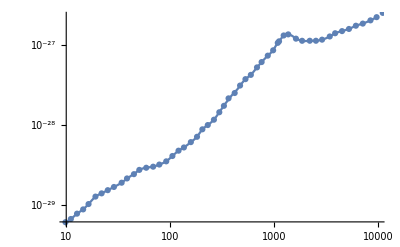

```mathematica
(**************************)
(***** M87 CDM Spike ******)
(**************************)
M87CDMSpikeData={{9.831 10^0,6.119 10^-30},
{1.108 10^1,6.709 10^-30},
{1.270 10^1,7.822 10^-30},
{1.455 10^1,8.844 10^-30},
{1.640 10^1,1.031 10^-29},
{1.912 10^1,1.278 10^-29},
{2.191 10^1,1.402 10^-29},
{2.512 10^1,1.537 10^-29},
{2.879 10^1,1.685 10^-29},
{3.415 10^1,1.905 10^-29},
{3.848 10^1,2.154 10^-29},
{4.486 10^1,2.436 10^-29},
{5.055 10^1,2.754 10^-29},
{5.893 10^1,2.929 10^-29},
{6.871 10^1,3.020 10^-29},
{7.876 10^1,3.211 10^-29},
{9.183 10^1,3.521 10^-29},
{1.053 10^2,4.105 10^-29},
{1.206 10^2,4.786 10^-29},
{1.359 10^2,5.248 10^-29},
{1.585 10^2,6.119 10^-29},
{1.817 10^2,7.134 10^-29},
{2.047 10^2,8.844 10^-29},
{2.307 10^2,1.000 10^-28},
{2.644 10^2,1.166 10^-28},
{2.979 10^2,1.445 10^-28},
{3.300 10^2,1.738 10^-28},
{3.656 10^2,2.154 10^-28},
{4.190 10^2,2.512 10^-28},
{4.721 10^2,3.114 10^-28},
{5.320 10^2,3.744 10^-28},
{5.995 10^2,4.233 10^-28},
{6.871 10^2,5.248 10^-28},
{7.612 10^2,6.119 10^-28},
{8.725 10^2,7.356 10^-28},
{9.831 10^2,8.577 10^-28},
{1.089 10^3,1.063 10^-27},
{1.120 10^3,1.110 10^-27},
{1.241 10^3,1.314 10^-27},
{1.374 10^3,1.356 10^-27},
{1.630 10^3,1.199 10^-27},
{1.868 10^3,1.128 10^-27},
{2.214 10^3,1.129 10^-27},
{2.538 10^3,1.129 10^-27},
{2.908 10^3,1.165 10^-27},
{3.448 10^3,1.277 10^-27},
{3.885 10^3,1.401 10^-27},
{4.529 10^3,1.490 10^-27},
{5.279 10^3,1.585 10^-27},
{6.154 10^3,1.739 10^-27},
{7.174 10^3,1.849 10^-27},
{8.506 10^3,2.029 10^-27},
{9.748 10^3,2.225 10^-27},
{1.117 10^4,2.516 10^-27}};
M87CDMSpike=Interpolation[M87CDMSpikeData];
Show[LogLogPlot[M87CDMSpike[x],{x,10,10000}],ListLogLogPlot[M87CDMSpikeData]]
```

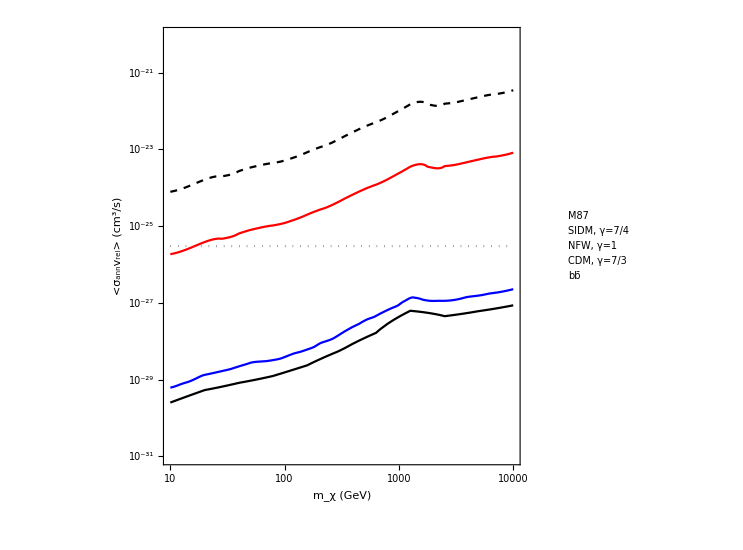

```mathematica
Show[LogLogPlot[XsectM87staralt[x],{x,10,10000},PlotStyle->{Red},PlotRange->{{10,10000},{10^-31, 9 10^-21}},PlotLegends-> Placed[LineLegend[{White},{"M87"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.5,0.93}],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],LogLogPlot[3 10^-26,{x,10,10000},PlotStyle->{Gray,Dotted},PlotLegends-> Placed[LineLegend[{White},{"SIDM, γ=7/4"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.59}]],LogLogPlot[XsectM87NFW[x],{x,10,10000},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{White},{"NFW, γ=1"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.72}]],(*LogLogPlot[XsectM87V3alt[x],{x,10,10000},PlotStyle->{Blue,Dashed}],*)(*LogLogPlot[M87Check[x],{x,10,10000},PlotStyle->{Blue,Dashed}],*)LogLogPlot[{M87Check[x],M87CDMSpike[x]},{x,10,10000},PlotStyle->{Black,Blue},PlotLegends-> Placed[LineLegend[{White},{"CDM, γ=7/3"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.26}]],(*LogLogPlot[XsectM87alt[x],{x,10,10000},PlotStyle->{Black,DotDashed},PlotLegends-> Placed[LineLegend[{White},{"CDM, γ=3/2"
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.68}]],*)LogLogPlot[1,{x,10,10000},PlotStyle->{White},PlotLegends-> Placed[LineLegend[{White},{Text[Style["bb̄",Italic]]
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.85,0.08}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.003],Black],FrameLabel-> {"m_χ (GeV)","<σ_annv_rel> (cm^3/s)"},LabelStyle->Directive[Black,FontSize-> 20],AspectRatio-> 1]
```

```mathematica
rspikeMW
```

0.0199257

```mathematica
PlotLegends-> Placed[LineLegend[{Black,{Black,DotDashed},{Black, Dotted},{Gray,DotDashed}},{"SIDM , γ = 7/4","CDM , γ = 3/2","No Spike","<σ_annv> = 3×10^-26 cm^3/s"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.3,0.25}]
```

PlotLegends→Placed[,{0.3,0.25}]

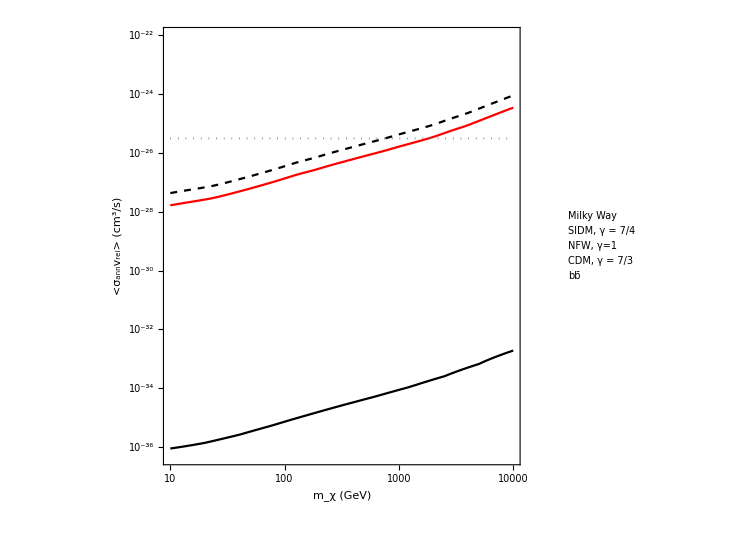

```mathematica
Show[LogLogPlot[XsectMWstaralt[x],{x,10,10000},PlotStyle->{Red},PlotRange->{{10,10000},{5 10^-37, 9 10^-23}},PlotLegends-> Placed[LineLegend[{White},{"Milky Way"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.5,0.93}],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],LogLogPlot[3 10^-26,{x,10,10000},PlotStyle->{Gray,Dotted},PlotLegends-> Placed[LineLegend[{White},{"SIDM, γ = 7/4"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.56}]],LogLogPlot[XsectMWNFW[x],{x,10,10000},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{White},{"NFW, γ=1"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.69}]],(*LogLogPlot[XsectMWCDM[x],{x,10,10000},PlotStyle->{Blue,Dotted}],*)(*LogLogPlot[XsectMWalt[x],{x,10,10000},PlotStyle->{Black,DotDashed}],*)LogLogPlot[MWCheck[x],{x,10,10000},PlotStyle->{Black},PlotLegends-> Placed[LineLegend[{White},{"CDM, γ = 7/3"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.15,0.13}]],(*LogLogPlot[XsectMWV3alt[x],{x,10,10000},PlotStyle->{Blue,Dashed}],*)LogLogPlot[1,{x,10,10000},PlotStyle->{White},PlotLegends-> Placed[LineLegend[{White},{Text[Style["bb̄",Italic]]
},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 25]],{0.85,0.08}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.003],Black],FrameLabel-> {"m_χ (GeV)","<σ_annv_rel> (cm^3/s)"},LabelStyle->Directive[Black,FontSize-> 20],AspectRatio-> 1]
```

```mathematica
rspikeMW
```

0.022

```mathematica
rspikeMWalt
```

0.00170329

```mathematica
(**********************)
(***** Gamma Plot *****)
(**********************)
stepgamma=(Log10[5/2]-Log10[3/2])/100;
stepgammain= Table[10^x,{x,Log10[3/2],Log10[5/2],stepgamma}];
stepgammainstarr =Table[10^x,{x,Log10[3/2]+8. stepgamma,Log10[5/2],stepgamma}];
```

```mathematica
M87XsectDatagamma= Table[{i,y/.limitM87star[100,i]} ,{i,stepgammainstarr}];
M87XsectDatagamma=Insert[M87XsectDatagamma,{3/2,y/.limitM87[100]},1];
(*M87XsectDatagamma=Insert[M87XsectDatagamma,{3/2 10^(1. stepgamma),(0.97)y/.limitM87[100]},2];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(2.stepgamma),(0.94)y/.limitM87[100]},3];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(3.stepgamma),(0.91)y/.limitM87[100]},4];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(4.stepgamma),(0.88)y/.limitM87[100]},5];*)
M87Xsectgamma=Interpolation[M87XsectDatagamma,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
M87XsectDatagammaalt= Table[{i,y/.limitM87staralt[100,i]} ,{i,stepgammainstarr}];
M87XsectDatagammaalt=Insert[M87XsectDatagammaalt,{3/2,y/.limitM87alt[100]},1];
(*M87XsectDatagamma=Insert[M87XsectDatagamma,{3/2 10^(1. stepgamma),(0.97)y/.limitM87[100]},2];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(2.stepgamma),(0.94)y/.limitM87[100]},3];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(3.stepgamma),(0.91)y/.limitM87[100]},4];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(4.stepgamma),(0.88)y/.limitM87[100]},5];*)
M87Xsectgammaalt=Interpolation[M87XsectDatagammaalt,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
MWXsectDatagamma= Table[{i,y/.limitMWstar[100,i]} ,{i,stepgammainstarr}];
MWXsectDatagamma=Insert[MWXsectDatagamma,{3/2,y/.limitMW[100]},1];
(*M87XsectDatagamma=Insert[M87XsectDatagamma,{3/2 10^(1. stepgamma),(0.97)y/.limitM87[100]},2];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(2.stepgamma),(0.94)y/.limitM87[100]},3];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(3.stepgamma),(0.91)y/.limitM87[100]},4];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(4.stepgamma),(0.88)y/.limitM87[100]},5];*)
MWXsectgamma=Interpolation[MWXsectDatagamma,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
MWXsectDatagammaalt= Table[{i,y/.limitMWstaralt[100,i]} ,{i,stepgammainstarr}];
MWXsectDatagammaalt=Insert[MWXsectDatagammaalt,{3/2,y/.limitMWalt[100]},1];
(*M87XsectDatagamma=Insert[M87XsectDatagamma,{3/2 10^(1. stepgamma),(0.97)y/.limitM87[100]},2];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(2.stepgamma),(0.94)y/.limitM87[100]},3];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(3.stepgamma),(0.91)y/.limitM87[100]},4];
M87XsectDatagamma=Insert[DracoXsectDatagamma,{3/2 10^(4.stepgamma),(0.88)y/.limitM87[100]},5];*)
MWXsectgammaalt=Interpolation[MWXsectDatagammaalt,InterpolationOrder->1]
```

InterpolatingFunction[…]

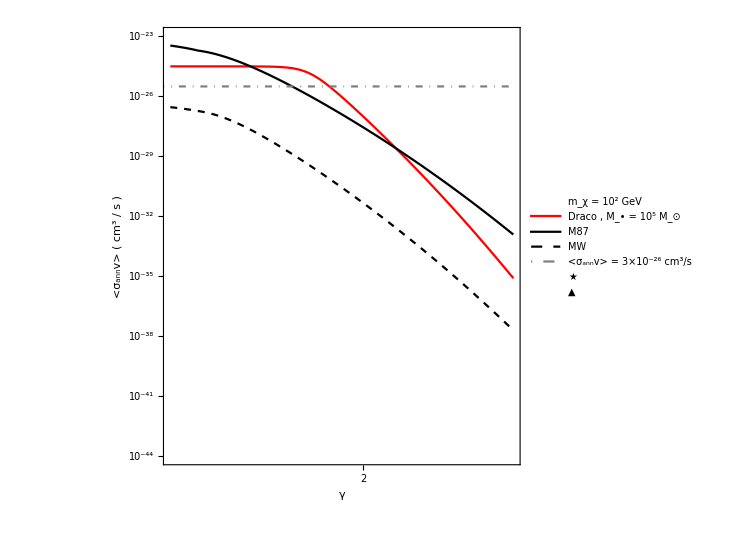

```mathematica
Show[LogLogPlot[ISODracoXsectgammaV2alt[x],{x,3/2,5/2},PlotRange->{{1.5,2.5},{10^-44,10^-23}},PlotStyle->Red,PlotLegends-> Placed[LineLegend[{White,Red,Black,{Black,Dashed},{Gray ,DotDashed}},{"m_χ = 10^2 GeV ","Draco , M_• = 10^5 M_⊙","M87","MW","<σ_annv> = 3×10^-26 cm^3/s"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 17]],{0.35,0.45}],FrameTicks->{{PowerTicks4[True],Automatic},{Automatic,Automatic}}],LogLogPlot[M87Xsectgammaalt[x],{x,3/2,5/2},PlotStyle->Black],
LogLogPlot[MWXsectgammaalt[x],{x,3/2,5/2},PlotStyle->{Black,Dashed}],LogLogPlot[3 10^-26,{x,3/3,5/2},PlotStyle->{Gray,DotDashed},PlotLegends-> Placed[LineLegend[{White},{"★"},LabelStyle->Directive[FontSize-> 17] ],{0.001,0.925}]],LogLogPlot[10^-50,{x,3/3,5/3},PlotStyle->{White,DotDashed},PlotLegends-> Placed[LineLegend[{White},{"▲"},LabelStyle->Directive[FontSize-> 17] ],{0.25,0.89}]],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"γ","<σ_annv> ( cm^3 / s )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

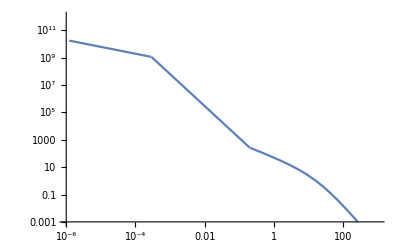

```mathematica
M87Profile[r_,x_,y_]:=Piecewise[{{0,r< 2 rschM87},{M87NFW[rspikeM87](rspikeM87/rannM87[x,y])^(7/3)(rannM87[x,y]/r)^(1/2),2 rschM87≤ r<rannM87[x,y]},{M87NFW[rspikeM87](rspikeM87/r)^(7/3), rannM87[x,y]≤ r<rspikeM87},{M87NFW[r],r≥ rspikeM87}}] 
LogLogPlot[(1/(3 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.8 10^-27(* kg / GeV *)))M87Profile[r,10, 3 10^-26],{r,10^-8,1000},PlotRange->{{10^-6,10^3},{10^-3,10^12}}]
```

```mathematica
radius[s_,θ_]:=√(DistM87^2+s^2-2DistM87 s Cos[θ]);
testFactor[θ_,x_,y_]:=NIntegrate[ M87Profile[radius[s,θ],x,y]^2,{s,DistM87-50,DistM87+50}]
```

```mathematica
checkFactor[x_,y_]:=2π NIntegrate[Sin[θ]testFactor[θ,x,y],{θ,0,π/180 1}]
```

```mathematica
CheckTestFactor=checkFactor[10, 5 10^(-30) ](1/(3 10^19(* m / kpc *)))^5(1/(100 (* cm /m *)))^5 (1.989 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.59887×10^-8}. NIntegrate obtained 3.35396×10^19 and 4.36526×10^18 for the integral and error estimates.

1.0589×10^27

```mathematica
checkSol[x_]:=NSolve[1/2 1/(4π)y/x^2 CheckTestFactor==fluxM87[x],y,Reals];
```

```mathematica
checkSol[10]
```

{{y→1.84831×10^-33}}

```mathematica
rspikeM87
```

0.2

```mathematica
rannM87[10,10^(-24)]
```

0.00129682

```mathematica
M87rs
```

20

```mathematica
M87rhos(1/(3.086 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.78 10^-27(* kg / GeV *)))
```

2.5

```mathematica
rhospike[r_]:=M87rhos(rspikeM87/M87rs)^-1(1-(2 rschM87)/r)^3(rspikeM87/r)^(7/3)(1/(3.086 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.78 10^-27(* kg / GeV *))); 
rhosat[x_,y_]:=x/(T y); 
checkDensity[r_,x_,y_]:= Piecewise[{{0,r<2rschM87},{(rhospike[r]rhosat[x,y])/(rhospike[r]+rhosat[x,y]),2rschM87≤ r<rspikeM87},{M87NFW[r](1/(3.086 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.78 10^-27(* kg / GeV *))),r≥ rspikeM87}}] ;
```

```mathematica
rhospike[rspikeM87]
```

249.995

```mathematica
checkDensity[0.1 rspikeM87,10,5 10^(-30)]
```

53851.

```mathematica
rhosat[10.,5 10^(-30)]
```

6.34196×10^12

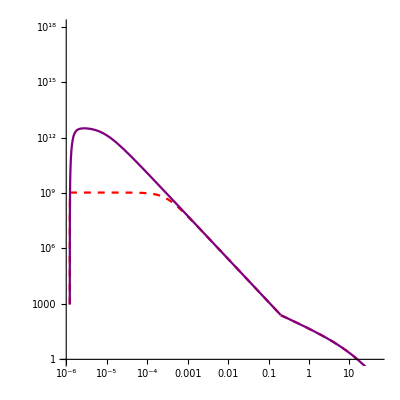

```mathematica
Show[LogLogPlot[checkDensity[r,10,3 10^-26],{r,10^-6,5 10^1},PlotRange->{{10^-6,5 10^1},{10^0,10^18}},PlotStyle->{Red,Dashed}], LogLogPlot[checkDensity[ r,10,6.7 10^-30],{r,10^-6,5 10^1},PlotStyle->Purple],AspectRatio-> 1]
```

```mathematica
rschM87
```

6.11664×10^-7

```mathematica
QCheck[x_,y_]:=NIntegrate[r^2 ((rhospike[r]rhosat[x,y])/(rhospike[r]+rhosat[x,y]))^2,{r,2rschM87,rspikeM87}]((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^-3;(* GeV^2 / cm^3 *)
```

```mathematica
QCheck[10,8 10^(-30)]
```

9.3×10^73

```mathematica
1/DistM87^2 QCheck[10,3 10^(-26)]((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^2
```

1.58776×10^20

```mathematica
dm=10000;
guess=8.61 10^(-28);
fluxM87[dm]/(1/(2 dm^2)1/DistM87^2 QCheck[dm,guess]((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^2)
```

8.61323×10^-28

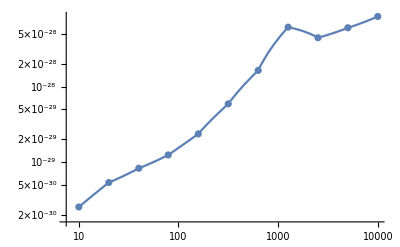

```mathematica
M87CheckData={{10,2.518 10^-30},
{20,5.328 10^-30},
{40,8.25 10^-30},
{79,1.24 10^-29},
{158,2.36 10^-29},
{316,5.927 10^-29},
{631,1.65 10^-28},
{1259,6.208 10^-28},
{2512,4.488 10^-28},
{5012,6.09 10^-28},
{10000,8.61 10^-28}};
M87Check=Interpolation[M87CheckData,InterpolationOrder->1];
Show[ListLogLogPlot[M87CheckData],LogLogPlot[M87Check[x],{x,10,10000}]]
```

```mathematica
stepcheck=(1.Log10[10000]-Log10[10])/10;
stepincheck= Table[10^x,{x,Log10[10],Log10[10000],stepcheck}]
```

{10.,19.9526,39.8107,79.4328,158.489,316.228,630.957,1258.93,2511.89,5011.87,10000.}

```mathematica
rhospikeMW[r_]:=MWrhos(rspikeMW/MWrs)^-1(1-(2 rschMW)/r)^3(rspikeMW/r)^(7/3)(1/(3.086 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.78 10^-27(* kg / GeV *))); 
QCheckMW[x_,y_]:=NIntegrate[r^2 ((rhospikeMW[r]rhosat[x,y])/(rhospikeMW[r]+rhosat[x,y]))^2,{r,2rschMW,rspikeMW}] ((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^-3;(* GeV^2 / cm^3 *)
```

```mathematica
checkDensityMW[r_,x_,y_]:= Piecewise[{{0,r<2rschMW},{(rhospikeMW[r]rhosat[x,y])/(rhospikeMW[r]+rhosat[x,y]),2rschMW≤ r<rspikeMW},{MWNFW[r](1/(3.086 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3 (1.989 10^30(* kg / msol *))(1/(1.78 10^-27(* kg / GeV *))),r≥ rspikeMW}}] ;
```

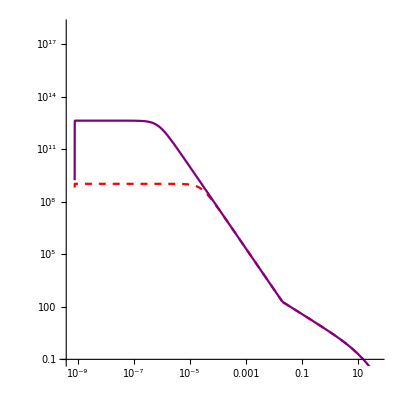

```mathematica
Show[LogLogPlot[checkDensityMW[r,10,3 10^-26],{r,rschMW,5 10^1},PlotRange->{{rschMW,5 10^1},{10^-1,10^18}},PlotStyle->{Red,Dashed}], LogLogPlot[checkDensityMW[ r,10,7.4 10^-30],{r,rschMW,5 10^1},PlotStyle->Purple],AspectRatio-> 1]
```

```mathematica
dm=10000;
guess=1.929 10^(-33);
fluxMW[dm]/(1/(2 dm^2)1/DistMW^2 QCheckMW[dm,guess]((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^2)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.9904×10^-9}. NIntegrate obtained 2.08535×10^10 and 24796.2 for the integral and error estimates.

1.92886×10^-33

```mathematica
100/dm^2 1/DistMW^2 QCheckMW[dm,guess]((1/(3.086 10^19(* m / kpc *)))(1/(100 (* cm /m *))))^2
```

3.27505×10^29

```mathematica
QCheckMW[dm,guess]
```

1.99613×10^74

```mathematica
QCheck[dm,guess]
```

7.3957×10^73

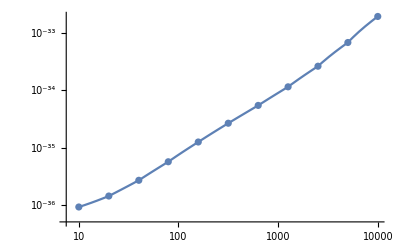

```mathematica
MWCheckData={{10,9.209 10^-37},
{20,1.43 10^-36},
{40,2.688 10^-36},
{79,5.656 10^-36},
{158,1.25 10^-35},
{316,2.656 10^-35},
{631,5.43 10^-35},
{1259,1.145 10^-34},
{2512,2.618 10^-34},
{5012,6.78 10^-34},
{10000,1.929 10^-33}};
MWCheck=Interpolation[MWCheckData,InterpolationOrder->1];
Show[ListLogLogPlot[MWCheckData],LogLogPlot[MWCheck[x],{x,10,10000}]]
```

```mathematica
rspikeMW
```

0.0199257

```mathematica
rspikeMWalt
```

0.00170329

```mathematica
rspikeM87
```

0.2

```mathematica
rspikeM87alt
```

0.271419

```mathematica
mx=10;
(* Mblackhole = 10 msol *)
xsectann=3 10^-26(*2.3 10^-35*);
rhoann=(mx(*GeV*)((1.989 10^30(* kg / msol *))^-1(1.8 10^-27(* kg / GeV *))))/(T(* s *) xsectann(*cm^3 / s*)((1/(3 10^19(* m / kpc *)))^3(1/(100 (* cm /m *)))^3));(*Msol / kpc^3 : 3.4x10^(25)*)
DracoSpikeRadius=0.000046(*0.0062*)(*kpc*);
DracoSpikeDensity=6.6 10^11(*4.8 10^9*)(*Msol/kpc^3*);
rannDraco=DracoSpikeRadius(DracoSpikeDensity/rhoann)^(3/7);(*kpc: 1x10^(-9)*)
QDracocheck=4π NIntegrate[r^2(DracoSpikeDensity(DracoSpikeRadius/r)^(7/3))^2,{r,rannDraco,DracoSpikeRadius}];(*Msol^2/kpc^3: 8.6x10^(24)*);
4/3 π (rannDraco^3-(2 rschDraco[10^1])^3)rhoann^2(*Msol^2/kpc^3: 4.8x10^(24)*);
(QDracocheck+4/3 π (rannDraco^3-(2 rschDraco[10^1])^3)rhoann^2+9.5 10^(11)76^(2)/(4π))/(QDracocheck+9.5 10^(11)76^(2)/(4π))
```

1.32381